```mathematica
MemoryInUse[]/10^6//IntegerPart
```

27

```mathematica
memory={};
```

```mathematica
Do[
mem=MemoryInUse[]/10^6//IntegerPart;
AppendTo[memory,mem];
ClearSystemCache[];
Print["Before: MemoryInUse (MB)",mem];
Timing[{EE[i],U[i]}=DiagH[20,3,1]][[1]]//Print;
,{i,1,5}];
memory
```

Before: MemoryInUse (MB)318

Eigensystem::arh: Because finding 1351 out of the 1351 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

1.4366

Before: MemoryInUse (MB)317

Eigensystem::arh: Because finding 1351 out of the 1351 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

1.9813

{40,56,70,85,99,114,129,143,158,173,187,187,187,187,187,187,187,187,187,187,202,202,202,202,202,202,202,202,202,202,217,217,217,217,217,217,217,217,217,217,231,231,231,231,231,231,231,231,231,231,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,260,275,275,275,275,275,275,275,275,275,275,292,292,292,292,292,292,292,292,292,292,318,317}

```mathematica
x=Table[Table[Timing[DiagH[10,m,1]][[1]],{i,1,20}],{m,0,5}]
```

Eigensystem::arh: Because finding 176 out of the 176 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

{{0.000049,0.00002,0.000018,0.000018,0.000018,0.000018,0.000017,0.000018,0.000017,0.000017,0.000015,0.000017,0.000016,0.000017,0.000017,0.000017,0.000017,0.000018,0.000016,0.000016},{0.000556,0.000426,0.000383,0.00038,0.000385,0.000381,0.000375,0.000374,0.000373,0.00037,0.000372,0.000372,0.000404,0.00037,0.00037,0.00036,0.00036,0.00036,0.000359,0.000358},{0.003065,0.009881,0.00992,0.009882,0.00945,0.009929,0.009935,0.009894,0.009894,0.009901,0.009921,0.009897,0.009978,0.009923,0.009916,0.009886,0.009875,0.009897,0.009878,0.009893},{0.362905,0.36551,0.478512,0.081061,0.07647,0.076077,0.075675,0.090699,0.076248,0.076267,0.075657,0.076166,0.075763,0.076726,0.075872,0.07625,0.075772,0.076179,0.075652,0.07614},{0.274588,0.270136,0.269566,0.270946,0.273792,0.271131,0.271382,0.273326,0.272336,0.273509,0.272505,0.270399,0.271411,0.272112,0.271403,0.269004,0.271405,0.270484,0.288836,0.282022},{1.07969,1.06888,1.06691,1.06911,1.06929,1.06869,1.07653,1.0767,1.07315,1.06734,1.06885,1.06975,1.06952,1.07583,1.07378,1.07464,1.07834,1.07165,1.07453,1.07399}}

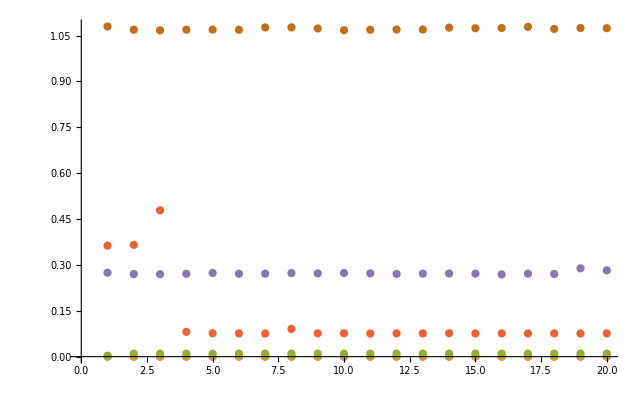

```mathematica
ListPlot[x]
```